```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[3,1]]]/2;
frames=Length[t[[2]]];
times=Flatten[t[[2]]];
positions={};
Do[
posSet=t[[3,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
```

```mathematica
TlistNVT={0.002,0.0025,0.0031};
```

```mathematica
TstringNVT=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistNVT
```

{0.00200000,0.00250000,0.00310000}

```mathematica
Tlist1024={0.002,0.0025,0.0031,0.01, 0.01584893, 0.02511886 ,0.03981072, 0.06309573};
```

```mathematica
Tstring1024=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistNVT
```

{0.00200000,0.00250000,0.00310000}

```mathematica
sytemsize={512,1024,4096};
```

```mathematica
timeNVT=Table[Table[testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
test=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N512/nvt_N512_p3.800_T0.00200000_0.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/postion→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
test[[6,1,1]]
```

0.0509407

```mathematica
cageRelativeMSDNVT=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_CRMSD_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
Dimensions[cageRelativeMSDNVT]
```

{3,3,35}

```mathematica
VelCorNVT=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_VelCor_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
CRSISFNVT=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_CRSISF_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
MSDNVT=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_MSD_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
SISFNVT=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[n]]],"/nvt_SISF_N",ToString[sytemsize[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
CRMSD512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_CRMSD_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
CRMSD512Mean=Table[Table[Mean[Table[CRMSD512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
MSD512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_MSD_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
MSD512Mean=Table[Table[Mean[Table[MSD512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
SISF512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_SISF_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
SISF512Mean=Table[Table[Mean[Table[SISF512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
MSD1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[2]]],"/nvt_MSD_N",ToString[sytemsize[[2]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,2}],{i,Length[TstringNVT]}];
```

```mathematica
MSD1024Mean=Table[Table[Mean[Table[MSD1024[[i,idx]][[time]],{idx,3}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
CRSISF512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_CRSISF_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
VelCor512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_VelCor_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
VelCor512Mean=Table[Table[Mean[Table[VelCor512[[i,idx]][[time]],{idx,9}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
VelCor1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[sytemsize[[1]]],"/nvt_VelCor_N",ToString[sytemsize[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[Tstring1024]}];
```

```mathematica
VelCor512Mean=Table[Table[Mean[Table[VelCor512[[i,idx]][[time]],{idx,9}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
Dimensions[CRSISF512]
```

{3,3,35}

```mathematica
CRSISF512Mean=Table[Table[Mean[Table[CRSISF512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

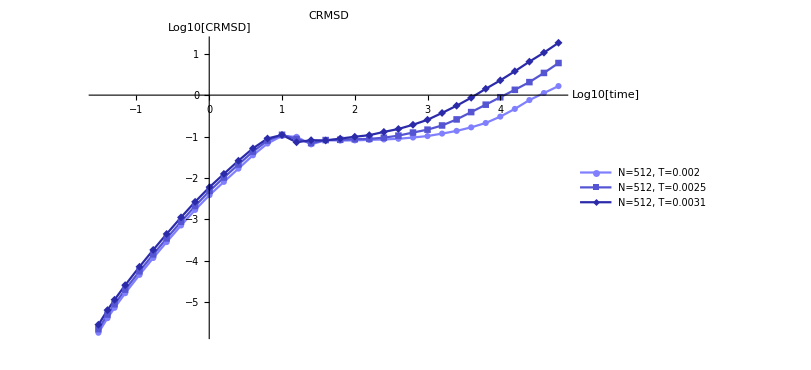

```mathematica
CRSISFplotNVT512=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[CRMSD512Mean[[i,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[0,0,1]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=512, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[CRMSD]"},ImageSize->600,PlotLabel->"CRMSD",PlotRange->Automatic]
```

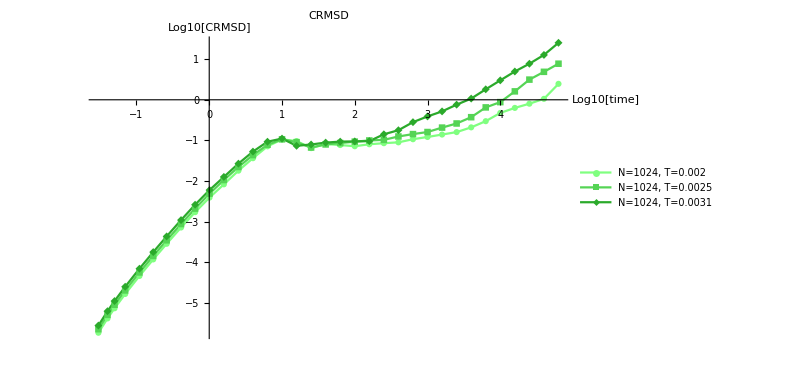

```mathematica
CRSISFplotNVT1024=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[cageRelativeMSDNVT[[i,2,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[0,1,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=1024, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[CRMSD]"},ImageSize->600,PlotLabel->"CRMSD",PlotRange->Automatic]
```

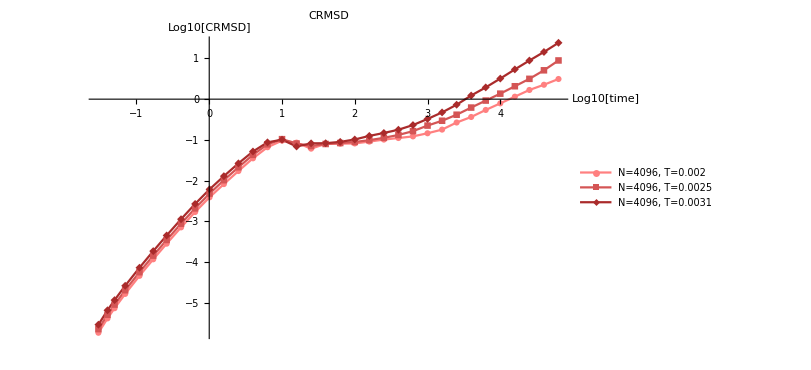

```mathematica
CRSISFplotNVT4096=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[cageRelativeMSDNVT[[i,3,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=4096, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[CRMSD]"},ImageSize->600,PlotLabel->"CRMSD",PlotRange->Automatic]
```

```mathematica
Show[CRSISFplotNVT4096,CRSISFplotNVT1024,CRSISFplotNVT512]
```

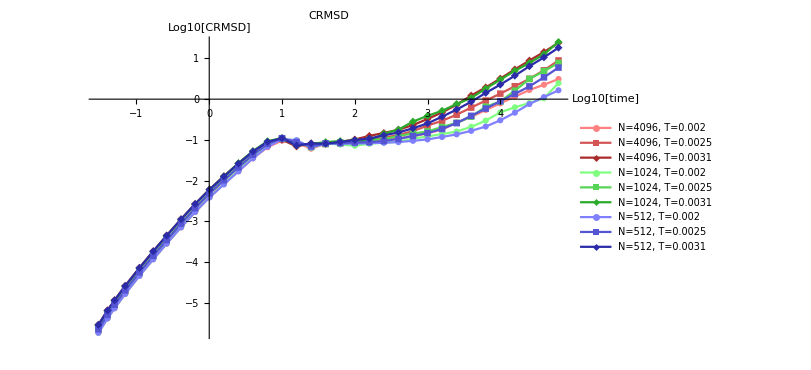

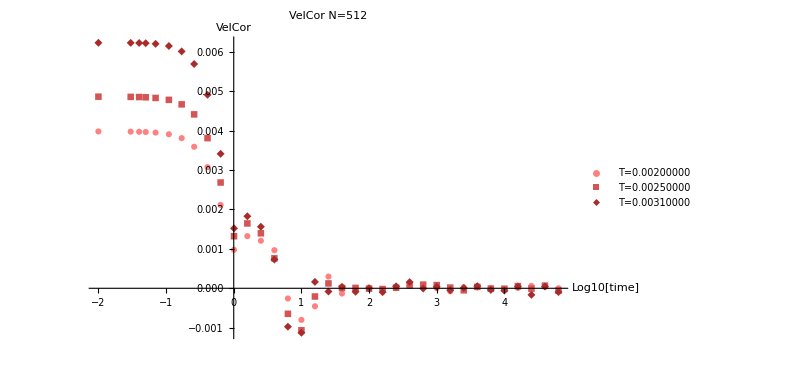

```mathematica
CRSISFplotNVT512=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],VelCor512Mean[[i,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",TstringNVT[[i]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","VelCor"},ImageSize->600,PlotLabel->"VelCor N=512",PlotRange->Automatic]
```

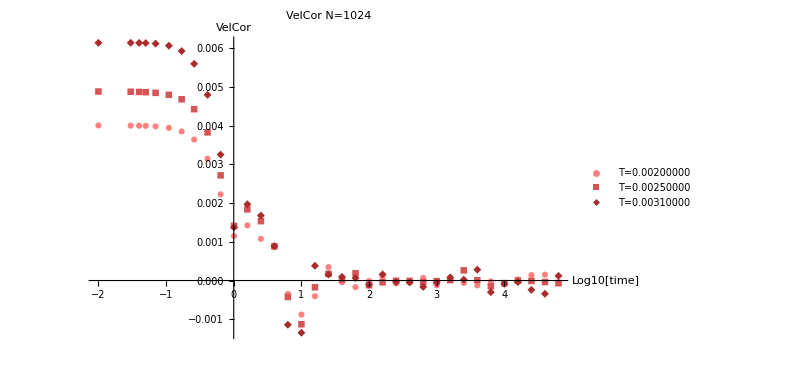

```mathematica
CRSISFplotNVT1024=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],VelCorNVT[[i,2,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",TstringNVT[[i]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","VelCor"},ImageSize->600,PlotLabel->"VelCor N=1024",PlotRange->Automatic]
```

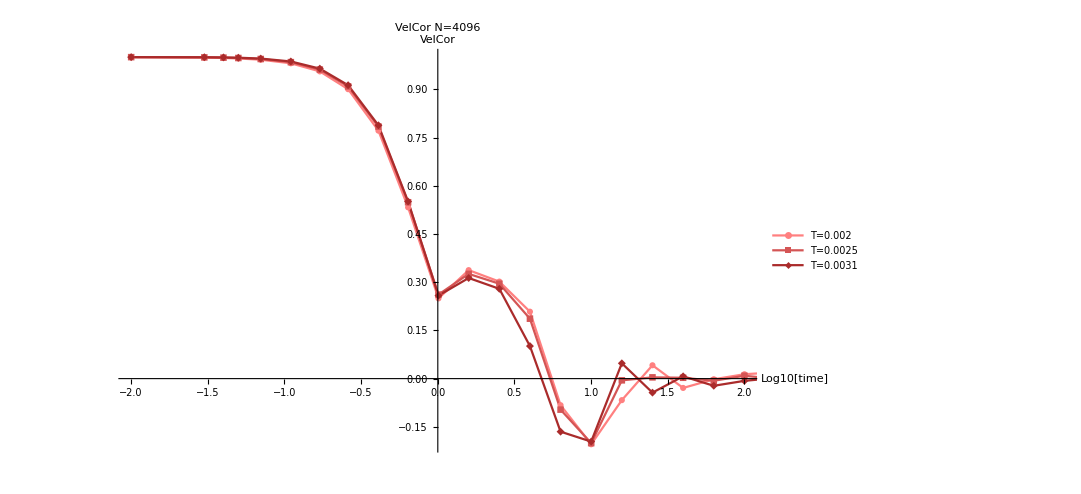

```mathematica
CRSISFplotNVT4096=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],VelCorNVT[[i,3,rec]]/VelCorNVT[[i,3,1]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","VelCor"},ImageSize->800,PlotLabel->"VelCor N=4096",PlotRange->{{-2,2},Automatic}]
```

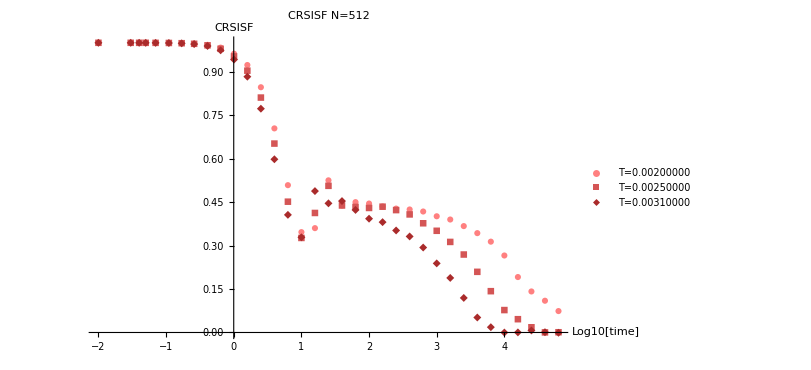

```mathematica
CRSISFplotNVT512=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],CRSISF512Mean[[i,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",TstringNVT[[i]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","CRSISF"},ImageSize->600,PlotLabel->"CRSISF N=512",PlotRange->Automatic]
```

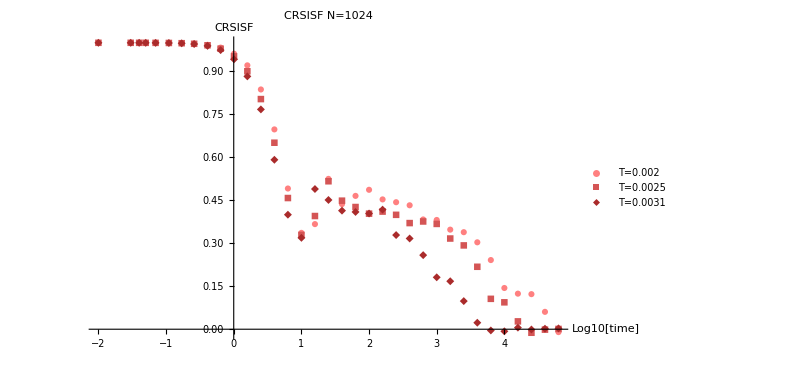

```mathematica
CRSISFplotNVT1024=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],CRSISFNVT[[i,2,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","CRSISF"},ImageSize->600,PlotLabel->"CRSISF N=1024",PlotRange->Automatic]
```

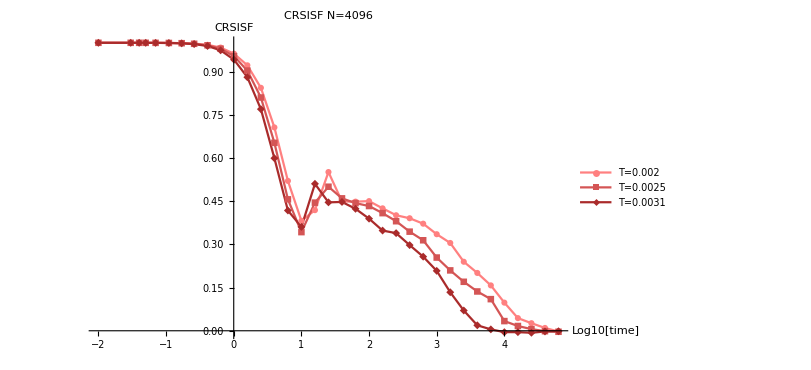

```mathematica
CRSISFplotNVT4096=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],CRSISFNVT[[i,3,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","CRSISF"},ImageSize->600,PlotLabel->"CRSISF N=4096",PlotRange->Automatic]
```

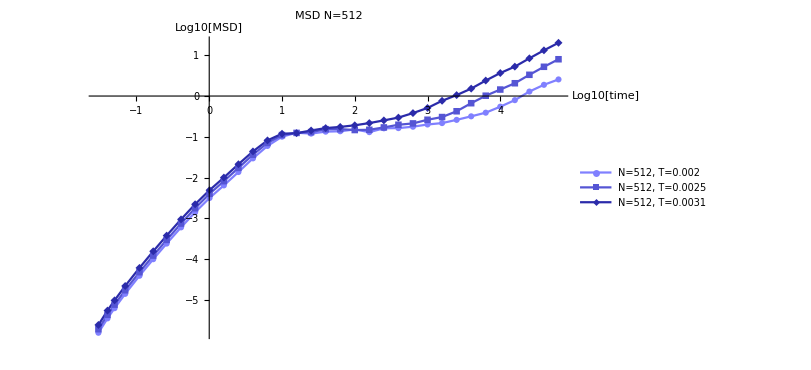

```mathematica
MSD512Plot=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[MSD512Mean[[i,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[0,0,1]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=512, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[MSD]"},ImageSize->600,PlotLabel->"MSD N=512",PlotRange->Automatic]
```

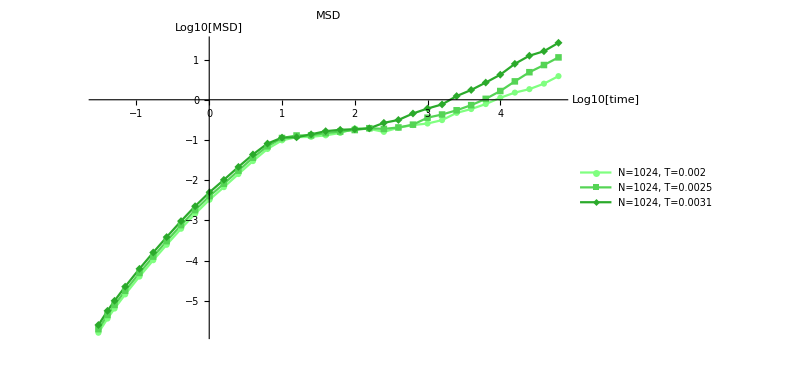

```mathematica
MSDplotNVT1024=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[MSD1024Mean[[i,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[0,1,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=1024, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[MSD]"},ImageSize->600,PlotLabel->"MSD",PlotRange->Automatic]
```

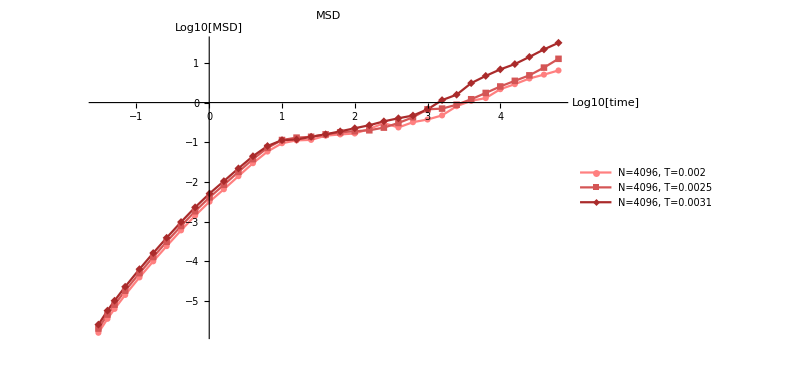

```mathematica
MSDplotNVT4096=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],Log10[MSDNVT[[i,3,rec]]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=4096, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[MSD]"},ImageSize->600,PlotLabel->"MSD",PlotRange->Automatic]
```

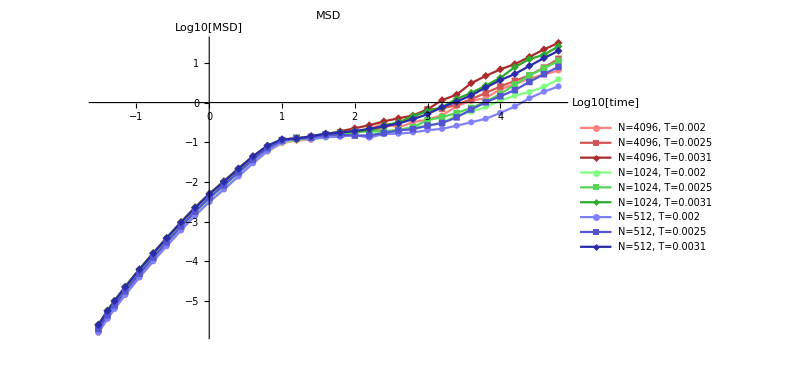

```mathematica
Show[MSDplotNVT4096,MSDplotNVT1024,MSD512Plot]
```

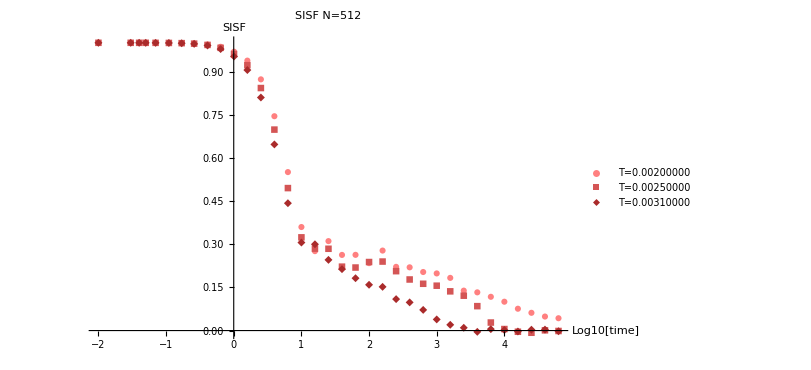

```mathematica
SISFplotNVT512=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],SISF512Mean[[i,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,1,3}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",TstringNVT[[i]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","SISF"},ImageSize->600,PlotLabel->"SISF N=512",PlotRange->Automatic]
```

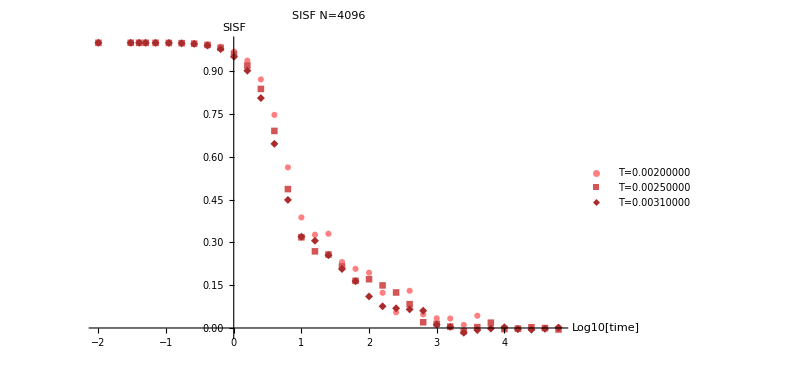

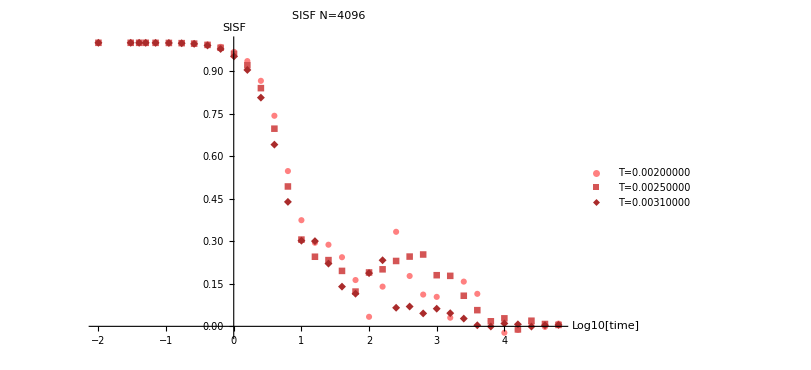

-Graphics-

-Graphics-

```mathematica
SISFplotNVT1024=ListPlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],SISFNVT[[i,3,rec]]},{rec,Length[cageRelativeMSDNVT[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",TstringNVT[[i]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","SISF"},ImageSize->600,PlotLabel->"SISF N=4096",PlotRange->Automatic]
```